```mathematica
dir="D:\\newLight3"
```

D:\newLight3

```mathematica
cell=0;
GetAltitude[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Cases[{"pt","y"}/.items,{cell,y_}->y]
]
```

```mathematica
fMin=0;
fMax=410000;
df=10000(*Ceiling[(fMax-fMin)/1000]10;*)
yMax=200;
dy=1;
frames=Table[frame,{frame,fMin,fMax,df}];
data=ParallelMap[BinCounts[GetAltitude[#],{0,yMax,dy}]&,frames];
```

10000

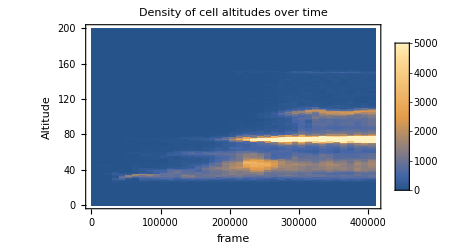

```mathematica
ListDensityPlot[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
FrameLabel->{"frame","Altitude"},
ClippingStyle->Automatic,
PlotRange->5000,
PlotLegends->Placed[Automatic,Right],
InterpolationOrder->0,
AspectRatio->1/GoldenRatio,
PlotLabel->"Density of cell altitudes over time"
]
```

```mathematica
BinCounts[GetAltitude[fMax]]
```

{1,0,0,2,3,2,0,1,0,0,0,0,0,0,0,1,2,0,0,1,1,5,0,0,0,0,2,3,3,1,8,14,26,37,203,464,688,891,10162,9234,2499}

```mathematica
ListPlot3D[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
AxesLabel->{"frame","Altitude","Density of cell altitudes"},
PlotRange->Full,
BoxRatios->{4,1,1},
ColorFunction->"DarkRainbow"]
```

-Graphics3D-